```mathematica
Qfield[x_]:=(*Piecewise[{{{0,0},First@x==0 && Last@x==0},{*)(({{0, -1}, {1, 0}}).x)/(2π Max[x.x,0.001])(*,True}}]*)
```

```mathematica
Vinf={1,0};
```

```mathematica
ν=(*1/1000*)10^-5;τ=0.01;eps=0.0001;
```

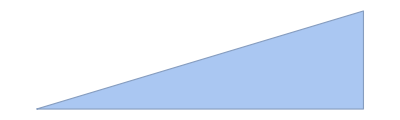

```mathematica
Rdots={{-1,-0.1},(*{0,0.2},*){1,1/2},(*{1,0.2},*){1,-0.1}(*,{0,-0.1}*)};
Rarea=BoundaryMeshRegion[Rdots,Line[{1,2,3,1}]]
```

```mathematica
Rmids=(RotateLeft@Rdots+Rdots)/2;
Rsides=(RotateLeft@Rdots-Rdots);
```

```mathematica
Rnormals=Transpose@(({{0, -1}, {1, 0}}).Transpose@Rsides);
```

```mathematica
Rnormals=Table[Rnormals[[i]]/(√(Rnormals[[i]].Rnormals[[i]])),{i,Length@Rnormals}];
```

```mathematica
curlDeploy=1.05Rdots;
```

```mathematica
(*вычисление рождений вихрей*)
```

```mathematica
L1=Table[Qfield[Rmids[[i]]-curlDeploy[[j]]].Rnormals[[i]],{i,1,Length@Rdots},{j,1,Length@Rdots}];
newGamma=Table[{G[i]},{i,1,Length@Rdots}];
f0=Rnormals.Vinf;
solution=Solve[{L1.newGamma+r==-f0,Sum[newGamma[[i]],{i,Length@newGamma}]==0},Append[First@Transpose@newGamma,r]]
```

{{G[1]→0.54517,G[2]→-1.39948,G[3]→0.854305,r→0.109775}}

```mathematica
(*по-хорошему на данном этапе нужно перекидывать новые вихри в единую пачку с остальными, но пока что мы этого делать не будем, потому что такой пачки у нас нет)) *)
```

```mathematica
nGammaR=Append[First@Transpose@newGamma,r]/.First@solution
```

{0.54517,-1.39948,0.854305,0.109775}

```mathematica
minCurl=0.001Max[Abs@nGammaR]
```

0.00139948

```mathematica
Vfield=Vinf+Sum[nGammaR[[i]]Qfield[{x,y}-curlDeploy[[i]]],{i,Length@nGammaR-1}];
```

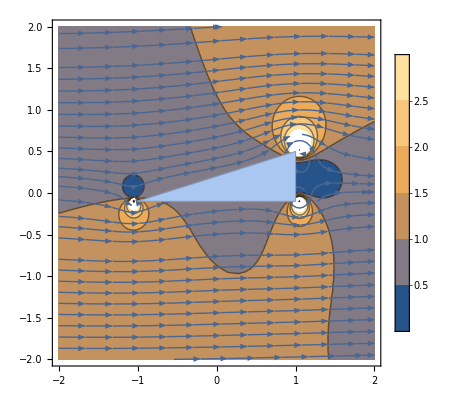

```mathematica
Show[ContourPlot[Vfield.Vfield,{x,-2,2},{y,-2,2},PlotLegends->Automatic,PlotRange->{0,3}],StreamPlot[Vfield,{x,-2,2},{y,-2,2}(*,Mesh->5*)],Rarea]
```

```mathematica
(*далее будем рассматривать снос вихревых нитей. Для этого будет требоваться рассмотрение поля "полной скорости", а значит требуется рассмотреть ещё и диффузионную составляющую нашего поля скоростей. Согласно диссеру предполагается рассмотрение поля диффузионной скорости по средствам вспомогательных интегралов, вероятнее всего это и будет являться наиболее трудоёмкой частью алгоритма, за исключением разве что того, что будет требоваться рассмотрение всего "хвоста".

ToDo: рассмотреть нюансы вычисления диффузионной скорости вблизи поверхности панели. Составить два варианта боевого кода: один - по тупейно-влобовой теории, без учёта рекомендаций; второй - учтя, по возможности, все доступные рекомендации.
Если будет получаться слишком просто, то придумать как улучшить...)))*)
```

```mathematica
(*составим массив из переносимых вихревых нитей со структурой {завихрённость, {координаты}} *)
```

```mathematica
curlTab=Table[{nGammaR[[i]],curlDeploy[[i]]},{i,Length@curlDeploy}];
```

```mathematica
(*теперь проведём просчитаем шаг по времени. Для начала нужно посчитать диффузионную скорость потока. Нормали к панелям, которые мы определили выше направлены от тела в жидкость, а значит соотношения из диссера берутся с минусом*)
```

```mathematica
etaR=Table[{x,y}-Rmids[[i]],{i,Length@Rmids}]/eps;
modEtaR=Table[etaR[[i]].etaR[[i]],{i,Length@Rmids}];
```

```mathematica
primeR=Table[{x,y}-Last@(curlTab[[i]]),{i,Length@Rmids}];
modPrimeR=Table[primeR[[i]].primeR[[i]],{i,Length@Rmids}];
```

```mathematica
I2=-Sum[primeR[[i]]/(√modPrimeR[[i]] eps) First@(curlTab[[i]])Exp[-(√modPrimeR[[i]])/eps],{i,Length@curlTab}];
I1=Sum[First@(curlTab[[i]])Exp[-(√modPrimeR[[i]])/eps],{i,Length@curlTab}];
I3=-Sum[Rnormals[[i]]Exp[-√modEtaR[[i]]],{i,Length@Rnormals}];
I0=2π eps^2+Sum[(etaR[[i]].Rnormals[[i]])/modEtaR[[i]](√modEtaR[[i]]+1)Exp[-√modEtaR[[i]]] √(Rsides[[i]].Rsides[[i]]),{i,Length@Rnormals}];
```

```mathematica
Wfield=ν(-I2/I1+I3/I0);
```

```mathematica
Ufield[x0_]:=(Vfield+Wfield)/.{x->First@x0,y->Last@x0}
```

```mathematica
curlTabNew=Table[{First@curlTab[[i]],Last@(curlTab[[i]])+τ Ufield[Last@(curlTab[[i]])+eps/1000]},{i,Length@curlDeploy}]
```

{{0.54517,{-1.03958,-0.103967}},{-1.39948,{1.05844,0.526086}},{0.854305,{1.05717,-0.10388}}}

```mathematica
newVfield=Vinf+Sum[First@curlTabNew[[i]]Qfield[{x,y}-Last@curlTabNew[[i]]],{i,Length@curlTabNew}];
```

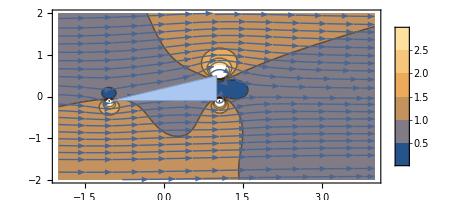

```mathematica
Show[ContourPlot[newVfield.newVfield,{x,-2,4},{y,-2,2},PlotLegends->Automatic,PlotRange->{0,3}],StreamPlot[newVfield,{x,-2,4},{y,-2,2}(*,Mesh->5*)],Rarea,AspectRatio->1/2]
```

```mathematica
pics={};
```

```mathematica
L1=Table[Qfield[Rmids[[i]]-curlDeploy[[j]]].Rnormals[[i]],{i,1,Length@Rdots},{j,1,Length@Rdots}];
newGamma=Table[{G[i]},{i,1,Length@Rdots}];
f0=Rnormals.Vinf;
```

```mathematica
For[n=0,n<10,n++,
For[t=0,t<3,t++,
f1=ParallelTable[Sum[Rnormals[[i]].Qfield[Rmids[[i]]-Last@curlTabNew[[m]]]First@curlTabNew[[m]],{m,1,Length@curlTabNew}],{i,1,Length@curlDeploy}];
solution=Solve[{L1.newGamma+r==-f0-f1,Sum[newGamma[[i]],{i,Length@newGamma}]==0},Append[First@Transpose@newGamma,r]];
nGammaR=Append[First@Transpose@newGamma,r]/.First@solution;
For[i=1,i≤Length@nGammaR-1,i++,AppendTo[curlTabNew,{nGammaR[[i]],curlDeploy[[i]]}]];
etaR=Table[{x,y}-Rmids[[i]],{i,Length@Rmids}]/eps;
modEtaR=Table[etaR[[i]].etaR[[i]],{i,Length@Rmids}];
primeR=Table[{x,y}-Last@(curlTab[[i]]),{i,Length@Rmids}];
modPrimeR=Table[primeR[[i]].primeR[[i]],{i,Length@Rmids}];
I2=-Parallelize@Sum[primeR[[i]]/(√modPrimeR[[i]] eps) First@(curlTab[[i]])Exp[-(√modPrimeR[[i]])/eps],{i,Length@curlTab}];
I1=Parallelize@Sum[First@(curlTab[[i]])Exp[-(√modPrimeR[[i]])/eps],{i,Length@curlTab}];
I3=-Parallelize@Sum[Rnormals[[i]]Exp[-√modEtaR[[i]]],{i,Length@Rnormals}];
(*I3=-Parallelize@Sum[Rnormals[[i]]eps (1-Exp[-(√(Rsides[[i]].Rsides[[i]]))/(2 eps)]),{i,Length@Rnormals}];*)
I0=2π eps^2+Parallelize@Sum[(etaR[[i]].Rnormals[[i]])/modEtaR[[i]](√modEtaR[[i]]+1)Exp[-√modEtaR[[i]]] √(Rsides[[i]].Rsides[[i]]),{i,Length@Rnormals}];
Wfield=ν(-I2/I1+I3/I0);
(*Ufield[x0_]:=(Vfield+Wfield)/.{x->First@x0,y->Last@x0}*)
curlTabNew=ParallelTable[{First@curlTabNew[[i]],Last@(curlTabNew[[i]])+τ (Vfield+Wfield)/.{x->First@Last@(curlTabNew[[i]])+eps/1000,y->Last@Last@(curlTabNew[[i]])+eps/1000}},{i,Length@curlTabNew}];
(*Определяем кандидатов под аннигиляцию и, пока есть такая возможность, без угрызений совести выпиливаем из списка*)
curlsToRemove={};
For[i=1,i<Length@curlTabNew,i++,If[RegionMember[Rarea,Last@(curlTabNew[[i]])] ||Abs@ First@(curlTabNew[[i]])<minCurl,AppendTo[curlsToRemove,{i}]];];
curlTabNew=Delete[curlTabNew,curlsToRemove];
(*определяем близкорасположенные вихри*)


Vfield=Vinf+Sum[First@curlTabNew[[i]]Qfield[{x,y}-Last@curlTabNew[[i]]],{i,Length@curlTabNew}];];
(*AppendTo[pics,Show[ContourPlot[Vfield.newVfield,{x,-2,4},{y,-2,2},PlotLegends->Automatic,PlotRange->{-1,3}],StreamPlot[Vfield,{x,-2,4},{y,-2,2}(*,Mesh->5*)],Rarea,AspectRatio->1/2]];*)
CurlsGraph=Table[Graphics[{White,Disk[Last@curlTabNew[[i]],1/20]}],{i,Length@curlTabNew}];
AppendTo[pics,Show[ContourPlot[0,{x,-2,4},{y,-2,2}],Rarea,CurlsGraph,AspectRatio->1/2]];
]
```

```mathematica
Length@pics
```

50

```mathematica
CurlsGraph=Table[Graphics[{White,Disk[Last@curlTabNew[[i]],1/20]}],{i,Length@curlTabNew}];
```

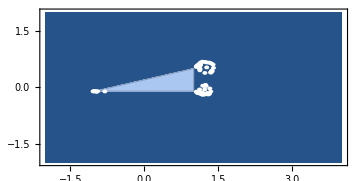

```mathematica
Show[ContourPlot[0,{x,-2,4},{y,-2,2}],Rarea,CurlsGraph,AspectRatio->1/2]
```

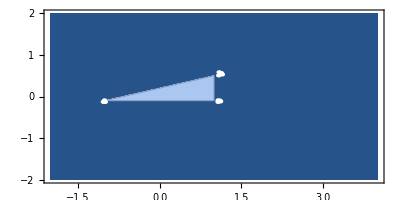

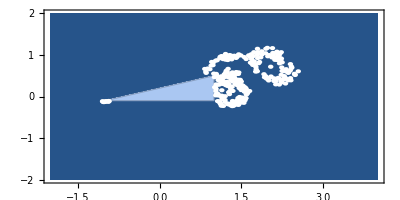

```mathematica
First@pics
Last@pics
```

```mathematica
Export["field_in_time.gif",pics]
```

field_in_time.gif

```mathematica
Last@curlTabNew
```

{0.0210971,{1.05439,-0.112912}}

```mathematica
Ufield[x0_]:=(Vfield+Wfield)/.{x->First@x0,y->Last@x0}
```

```mathematica
Ufield[{0,0}]
```

{0.860367,0.131664}

```mathematica
(Vfield+Wfield)/.{x->0,y->0}
```

{0.860367,0.131664}

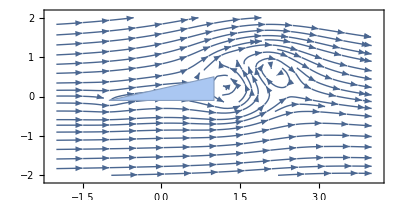

```mathematica
Show[StreamPlot[Vfield,{x,-2,4},{y,-2,2}(*,Mesh->5*)],Rarea,AspectRatio->1/2]
```

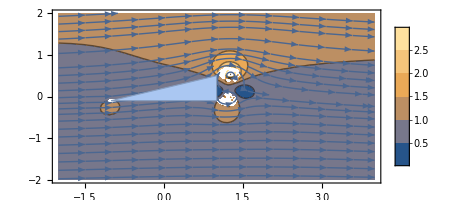

```mathematica
Show[ContourPlot[√((Vfield).(Vfield)),{x,-2,4},{y,-2,2},PlotLegends->Automatic,PlotRange->{0,3}],StreamPlot[Vfield,{x,-2,4},{y,-2,2}(*,Mesh->5*)],Rarea,AspectRatio->1/2]
```

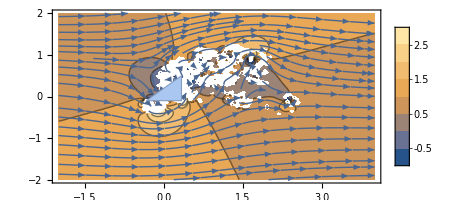

```mathematica
Show[ContourPlot[Vfield.newVfield,{x,-2,4},{y,-2,2},PlotLegends->Automatic,PlotRange->{-1,3}],StreamPlot[Vfield,{x,-2,4},{y,-2,2}(*,Mesh->5*)],Rarea,AspectRatio->1/2]
```